```mathematica
raw=Drop[Import[FileNameJoin[{NotebookDirectory[],"data/lid16/out100.dat"}], "Table", "FieldSeparators"->{" "}, HeaderLines->1], -1];
```

```mathematica
cdata=Transpose[{raw[[All, 8]], raw[[All, 9]], raw[[All, 10]]}];
vdata=Transpose[{raw[[All, 12]], raw[[All, 13]], raw[[All, 14]]}];
pdata=raw[[All, 16]];
```

```mathematica
avgv=Mean[Sqrt[vdata[[All, 1]]^2+vdata[[All,2]]^2+vdata[[All, 3]]^2]]
```

0.112115

```mathematica
maxv=Max[Abs[vdata]]
```

0.803255

```mathematica
l=Abs[Max[Flatten[cdata]]-Min[Flatten[cdata]]]
```

2.

```mathematica
nu=0.890*10^(-3)
```

0.00089

```mathematica
ren=avgv*l/nu
```

251.945

```mathematica
maxren=maxv*l/nu
```

1805.07

```mathematica
arrows=Table[{Arrowheads[.01],Arrow[{
cdata[[i]],cdata[[i]]+
(vdata[[i]]/(maxv))*l*0.4
}]}, {i, Length[raw]}];
```

```mathematica
gg=Graphics3D[arrows,Axes->True,AxesLabel->{"x (m)","y (m)","z (m)"},ImageSize->Large]
```

-Graphics3D-

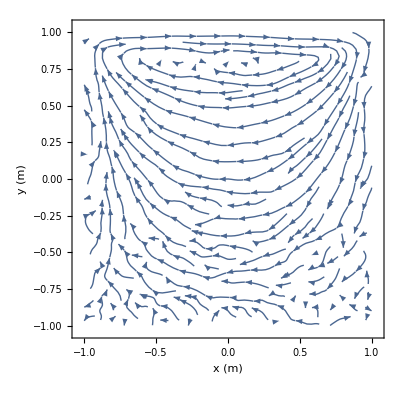

```mathematica
str=ListStreamPlot[Table[{{cdata[[i, 1]], cdata[[i, 2]]}, {vdata[[i, 1]], vdata[[i, 2]]}}, {i, Length[vdata]}], FrameLabel->{"x (m)","y (m)"}]
```

```mathematica
(*ListContourPlot3D[Transpose[{raw[[All, 8]], raw[[All, 9]], raw[[All, 10]], raw[[All, 16]]}], PlotRange->All, PlotLegends->Automatic]*)
```

```mathematica
(*ListDensityPlot3D[Transpose[{raw[[All, 8]], raw[[All, 9]], raw[[All, 10]], raw[[All, 16]]}],ColorFunction->"TemperatureMap",PlotLegends->BarLegend[All, LegendLabel->"p (Pa)"], PlotRange->All,AxesLabel->{"x (m)","y (m)","z (m)"}]*)
```

```mathematica
(*ListDensityPlot3D[Transpose[{raw[[All, 8]], raw[[All, 9]], raw[[All, 10]], Sqrt[raw[[All, 12]]^2+raw[[All, 13]]^2+raw[[All, 14]]^2]}],ColorFunction->"BlueGreenYellow",PlotLegends->Automatic, PlotRange->All]*)
```

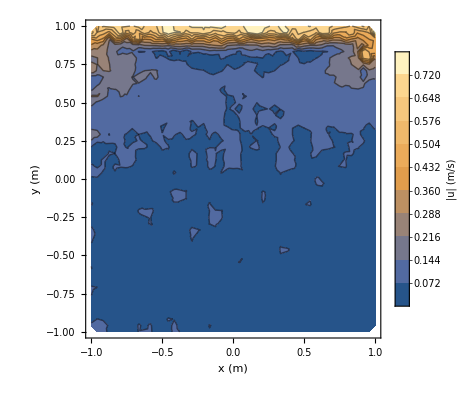

```mathematica
vmp=ListContourPlot[Transpose[{raw[[All, 8]], raw[[All, 9]], Sqrt[raw[[All, 12]]^2+raw[[All, 13]]^2+raw[[All, 14]]^2]}], PlotRange->All, PlotLegends->BarLegend[All, LegendLabel->"|u| (m/s)"], Contours->10, FrameLabel->{"x (m)", "y (m)"}]
```

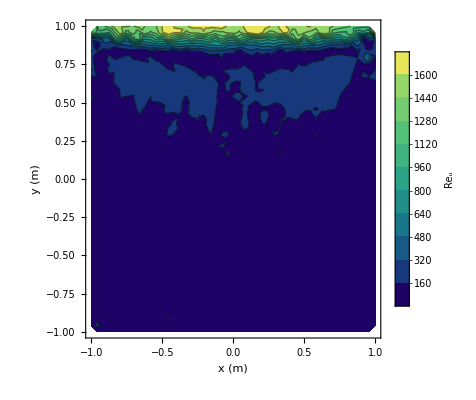

```mathematica
ListContourPlot[Transpose[{raw[[All, 8]], raw[[All, 9]], Abs[raw[[All, 12]]]*l/nu}], PlotRange->All, PlotLegends->BarLegend[All, LegendLabel->"Re_u"],ColorFunction->"BlueGreenYellow", Contours->10, FrameLabel->{"x (m)", "y (m)"}]
```

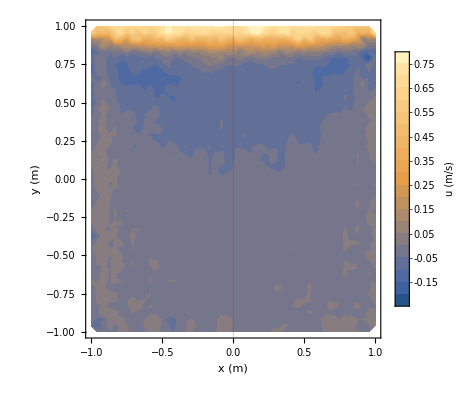

```mathematica
vxp=ListContourPlot[Transpose[{raw[[All, 8]], raw[[All, 9]], raw[[All, 12]]}], PlotRange->All, PlotLegends->BarLegend[All, LegendLabel->"u (m/s)"], Contours->20, ContourStyle->None, FrameLabel->{"x (m)", "y (m)"},
GridLines->{{{0,Red}},None}]
```

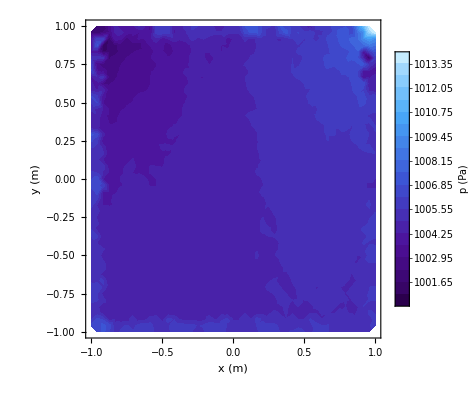

```mathematica
pxp=ListContourPlot[Transpose[{raw[[All, 8]], raw[[All, 9]], raw[[All, 16]]}], PlotRange->All, PlotLegends->BarLegend[Automatic, LegendLabel->"p (Pa)"], Contours->20, ContourStyle->None, FrameLabel->{"x (m)", "y (m)"},ColorFunction->"DeepSeaColors"]
```

```mathematica
c1=ImportString["\
itn 1 / 10, res 1.6803e+01, msi 1669
itn 2 / 10, res 2.6366e+01, msi 1669
itn 3 / 10, res 2.1336e+01, msi 1669
itn 4 / 10, res 1.1136e+01, msi 1669
itn 5 / 10, res 2.8367e+01, msi 1669
itn 6 / 10, res 3.0761e+01, msi 1669
itn 7 / 10, res 2.3498e+01, msi 1669
itn 8 / 10, res 1.4937e+01, msi 1669
itn 9 / 10, res 3.2906e+01, msi 1669
itn 10 / 10, res 4.5518e+01, msi 1669
", "Table", "FieldSeparators"->{" ", ","}][[All, 6]];
```

```mathematica
c1fit=Fit[c1, {1, x, 1/x}, x]
```

9.05877+8.16074/x+2.49341 x

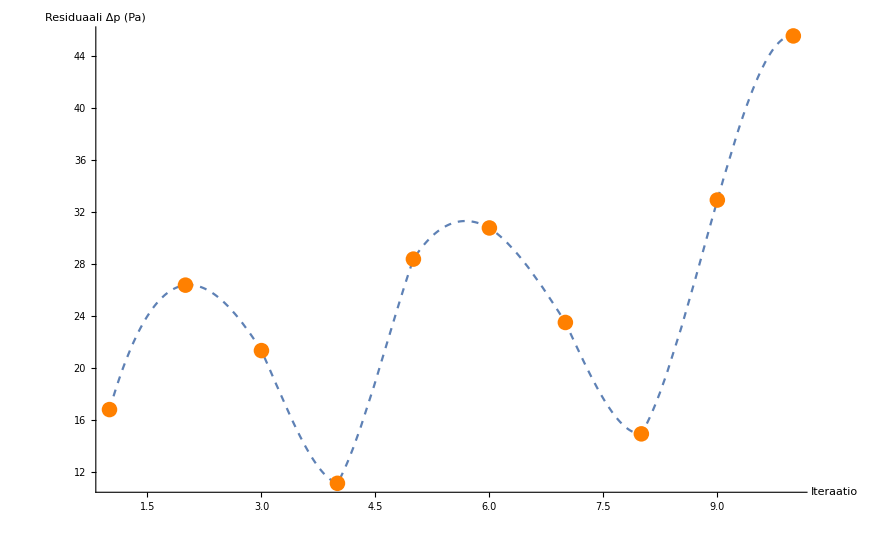

```mathematica
Show[(*Plot[c1fit, {x, 1, Length[c1]}, PlotStyle->LightGray, PlotRange->All],*)Plot[Interpolation[c1][x], {x, 1, Length[c1]}, PlotStyle->Dashed, PlotRange->All], ListPlot[c1, PlotStyle->Orange], AxesLabel->{"Iteraatio", "Residuaali Δp (Pa)"}, PlotRange->All, AxesOrigin->{1,0}]
```

```mathematica
Export["~/Dropbox/pxp.pdf", pxp];
```

```mathematica
Export["~/Dropbox/contour_vm.pdf", vmp];
```

```mathematica
Export["~/Dropbox/contour_vx.pdf", vxp];
```

```mathematica
Export["~/Dropbox/str.pdf", str];
```

```mathematica
Export["~/Dropbox/gg.pdf", gg];
```

```mathematica
ClearSystemCache[]
```

```mathematica
raw[[Ordering[Sqrt[raw[[All, 13]]^2+raw[[All, 13]]^2+raw[[All, 14]]^2], -1], All]]
```

{{o,0,t,0.01,f,1594,x,0.916667,0.833333,-0.103211,v,-0.113659,-0.554526,0.062048,p,1003.83}}